```mathematica
ClearAll["Global`*"]
```

```mathematica
FlipFlop[n_,i_,j_]:=Block[
{v=IntegerDigits[n,2,L]},
If[v[[i]]≠0&&v[[j]]≠1,
v[[i]]=v[[i]]-1;
v[[j]]=v[[j]]+1;
FromDigits[v,2]
,
-1]
]
Raise[n_,i_]:=Block[
{v=IntegerDigits[n,2,L]},
If[v[[Mod[i,L,1]]]≠1,
v[[i]]=v[[i]]+1;
FromDigits[v,2]
,
-1]
]
U[t_,e_,v_]:=Transpose[v].DiagonalMatrix[Exp[-ⅈ e t]].Conjugate[v]
sA[vec_,sitesA_]:=Block[
{M=SparseArray[Table[{FromDigits[IntegerDigits[i,2,L][[sitesA]],2]+1,FromDigits[IntegerDigits[i,2,L][[Complement[Range@L,sitesA]]],2]+1}->vec[[i+1]],{i,0,2^L-1}]],
l},
l=Sort[SingularValueList[M,Tolerance->0]];
-Sum[If[l[[i]]≠0,l[[i]]^2 Log[l[[i]]^2],0]
,{i,1,Length@l}]
]
```

```mathematica
L=5;
```

```mathematica
Id=IdentityMatrix[2^L];
Heis=Table[
SparseArray[
Flatten@Table[
Block[{h=FlipFlop[j,i,k],v=2IntegerDigits[j,2,L]-1},
If[h≠-1,
{{j+1,h+1}->2.,
{h+1,j+1}->2.,
{j+1,j+1}->N[v[[i]]*v[[k]]]},
{{j+1,j+1}->N[v[[i]]*v[[k]]]}]
]
,{j,0,2^L-1}]
,{2^L,2^L}]
,{i,1,L},{k,1,L}];

Sz=Monitor[Table[
SparseArray[
Table[
Block[{v=2IntegerDigits[j,2,L]-1},
{j+1,j+1}->N[v[[i]]]
]
,{j,0,2^L-1}]
,{2^L,2^L}]
,{i,1,L}],i];
SzTot=Sum[Sz[[i]],{i,L}];

Sp=Monitor[Table[
SparseArray[
DeleteCases[Table[
Block[{h=Raise[j,i]},
If[h≠-1,
{h+1,j+1}->1.]
]
,{j,0,2^L-1}]
,Null]
,{2^L,2^L}]
,{i,1,L}],i];
Sm=Monitor[Table[Transpose[Sp[[i]]]
,{i,1,L}],i];
```

```mathematica
IntegerDigits[#,2,L]&/@(Range[2^L]-1)
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

## Exact time evolution

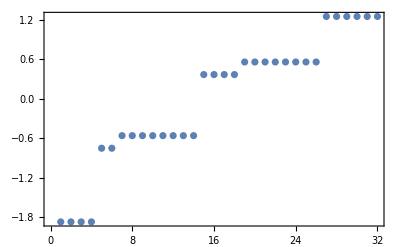

```mathematica
H=(Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L}])/4;
{e,v}=Eigensystem[H];
eigs=e[[Ordering[e]]];
vecs=v[[Ordering[e]]];
ListPlot[Chop@eigs,Frame->True]
```

```mathematica
MinMax@Chop[Conjugate[vecs].H.Transpose[vecs]-DiagonalMatrix[eigs]]
```

{0,0}

```mathematica
MatrixForm[H]
```

```mathematica
Chop[vecs[[1]]]
```

{0,0,0,-0.0335247,0,-0.0218309,0.0470169,0.126292,0,0.123092,-0.177336,0,0.0625827,-0.330637,0.204345,0,0,-0.0677363,0.163844,-0.126292,-0.0877687,0.534982,-0.534982,0,-0.00833867,-0.204345,0.330637,0,0,0,0,0}

```mathematica
tf=50(*/Jp*);
dt=tf/200;
Nt=IntegerPart[tf/dt];
```

```mathematica
c=Table[(1+(-1)^i)/2,{i,L}]
init=UnitVector[2^L,FromDigits[c,2]+1];
```

{0,1,0,1,0}

```mathematica
Table[init.Sz[[i]].init,{i,L}]
```

{-1.,1.,-1.,1.,-1.}

```mathematica
AbsoluteTiming[
(*u=U[dt,eigs,vecs];*)
revos=ConstantArray[0,Nt+1];
revos[[1]]=init;
Monitor[Do[
(*revos[[i+1]]=u.revos[[i]];*)
revos[[i+1]]=MatrixExp[-ⅈ(dt)H,revos[[i]]];
,{i,1,Nt}],i];
]
Szt=Table[{(t-1)dt,Conjugate[revos[[t]]].Sz[[1]].revos[[t]]/2},{t,1,Length@revos}];
```

{0.274461,Null}

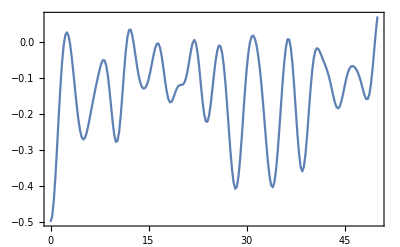

```mathematica
ListPlot[Szt,Frame->True,Joined->True,PlotRange->All]
```

```mathematica
(* Calculate Entanglement Entropy as a function of time *)
```

```mathematica
sitesA=Range[Floor[L/2]]; (* Define the set of sites for region A*)
```

```mathematica
sAList=Table[{(t-1)dt,sA[revos[[t]],sitesA]},{t,1,Length@revos}];
```

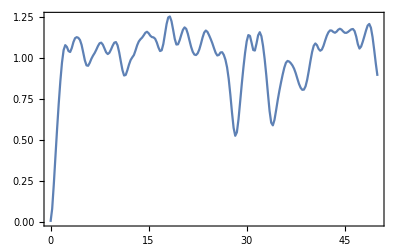

```mathematica
ListPlot[sAList,Frame->True,Joined->True,PlotRange->All]
```

## Trotter Evolution

```mathematica
δt=1
UOdd=MatrixExp[-ⅈ δt Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L,2}]/4];
UEven=MatrixExp[-ⅈ δt Sum[Heis[[i,Mod[i+1,L,1]]],{i,2,L,2}]/4];
```

1

```mathematica
Table[{i,Mod[i+1,L,1]},{i,1,L,2}]
Table[{i,Mod[i+1,L,1]},{i,2,L,2}]
```

{{1,2},{3,1}}

{{2,3}}

```mathematica
MatrixForm@Chop[(Heis[[1,2]]+Heis[[3,1]]).Heis[[2,3]]-Heis[[2,3]].(Heis[[1,2]]+Heis[[3,1]])]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
UTrotter=UEven.UOdd;
```

```mathematica
ψtrot={init};
Monitor[
Do[
AppendTo[ψtrot,UTrotter.ψtrot[[-1]]]
,{t,1,10}]
,t]
```

```mathematica
ψtrot[[-1]]
```

{0.+0. ⅈ,0.346635+0.312667 ⅈ,-2.77556×10^-17-0.625333 ⅈ,0.+0. ⅈ,-2.63678×10^-16-0.625333 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Chop[Table[Conjugate[ψtrot[[t]]].revos[[t]],{t,Length@revos}]]
```

```mathematica
TrotterEvolve[tf_,nt_,init_]:=Block[
{dt=N[tf/nt],UOdd,UEven,UTrotter,ψtrot},
UOdd=MatrixExp[-ⅈ dt Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L,2}]/4];
UEven=MatrixExp[-ⅈ dt Sum[Heis[[i,Mod[i+1,L,1]]],{i,2,L,2}]/4];
UTrotter=UEven.UOdd;
ψtrot={init};
Do[
AppendTo[ψtrot,UTrotter.ψtrot[[-1]]];
,{t,1,nt}];
ψtrot[[-1]]
]
```

```mathematica
TrotterEvolve[10,1000,init]
```

{0.+0. ⅈ,0.346635+0.312667 ⅈ,5.88028×10^-15-0.625333 ⅈ,0.+0. ⅈ,-6.50738×10^-15-0.625333 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
revos[[-1]]
```

{0.+0. ⅈ,0.346635+0.312667 ⅈ,-9.56353×10^-15-0.625333 ⅈ,0.+0. ⅈ,-2.7504×10^-15-0.625333 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
TrotterFixStepList={init};
Do[
AppendTo[TrotterFixStepList,TrotterEvolve[n*dt,10,init]],
{n,1,Nt}]
TrotterFixStepSz=Table[{(t-1)dt,Conjugate[TrotterFixStepList[[t]]].Sz[[1]].TrotterFixStepList[[t]]/2},{t,1,Length@TrotterFixStepList}];
```

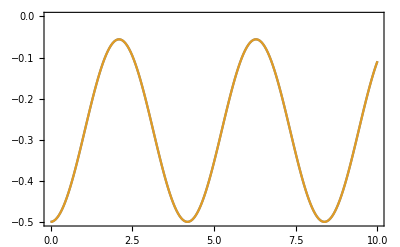

```mathematica
ListPlot[{Szt,TrotterFixStepSz},Joined->True,Frame->True]
```

## Ansatz

```mathematica
ψ[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_,θ9_,θ10_]:=MatrixExp[-ⅈ  θ10  Heis[[5,1]]].MatrixExp[-ⅈ  θ9  Heis[[4,5]]].MatrixExp[-ⅈ θ8 Heis[[3,4]]].MatrixExp[-ⅈ  θ7  Heis[[2,3]]].MatrixExp[-ⅈ  θ6  Heis[[1,2]]].MatrixExp[-ⅈ  θ5  Heis[[5,1]]].MatrixExp[-ⅈ  θ4  Heis[[4,5]]].MatrixExp[-ⅈ θ3 Heis[[3,4]]].MatrixExp[-ⅈ  θ2  Heis[[2,3]]].MatrixExp[-ⅈ  θ1  Heis[[1,2]]].init
```

```mathematica
ψ[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_,θ9_,θ10_]:=MatrixExp[-ⅈ θ10 Heis[[4,5]]].MatrixExp[-ⅈ θ9 Heis[[2,3]]].MatrixExp[-ⅈ θ8 Heis[[5,1]]].MatrixExp[-ⅈ θ7 Heis[[3,4]]].MatrixExp[-ⅈ θ6 Heis[[1,2]]].MatrixExp[-ⅈ θ5 Heis[[4,5]]].MatrixExp[-ⅈ θ4 Heis[[2,3]]].MatrixExp[-ⅈ θ3 Heis[[5,1]]].MatrixExp[-ⅈ θ2 Heis[[3,4]]].MatrixExp[-ⅈ θ1 Heis[[1,2]]].init
```

```mathematica
ψ[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_]:=MatrixExp[-ⅈ θ8 Heis[[4,1]]].MatrixExp[-ⅈ θ7 Heis[[2,3]]].MatrixExp[-ⅈ θ6 Heis[[3,4]]].MatrixExp[-ⅈ θ5 Heis[[1,2]]].MatrixExp[-ⅈ θ4 Heis[[4,1]]].MatrixExp[-ⅈ θ3 Heis[[2,3]]].MatrixExp[-ⅈ θ2 Heis[[3,4]]].MatrixExp[-ⅈ θ1 Heis[[1,2]]].init
```

```mathematica
foo[θSeq___]:=With[{θ={θSeq}},
Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[L+n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L}]]].init
]
```

```mathematica
foo[θSeq___]:=With[{θ={θSeq}},
Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[2L+n]]Heis[[n,Mod[n+1,L,1]]]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[2L+n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[L+n]]Heis[[n,Mod[n+1,L,1]]]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[L+n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[n]]Heis[[n,Mod[n+1,L,1]]]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L,2}]]].init
]
```

```mathematica
Table[{n,Mod[n+1,L,1]},{n,1,L,2}]
Table[{n,Mod[n+1,L,1]},{n,2,L,2}]
```

{{1,2},{3,4},{5,1}}

{{2,3},{4,5}}

```mathematica
vars=ToExpression[Table["θ"<>ToString[n],{n,1,3L}]]
```

{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9,θ10,θ11,θ12,θ13,θ14,θ15}

```mathematica
(*sol=NMinimize[1-Abs[Conjugate[revos[[-1]]].ψ[Sequence@@vars]],vars]*)
sol=NMinimize[1-Abs[Conjugate[revos[[200]]].foo[Sequence@@vars]],vars]
```

{8.7846×10^-6,{θ1→0.510415,θ2→-0.26986,θ3→0.115392,θ4→0.483381,θ5→-0.878111,θ6→0.213791,θ7→0.539192,θ8→0.331815,θ9→-0.40385,θ10→-0.480584,θ11→-0.253483,θ12→-0.041039,θ13→0.327869,θ14→-1.01667,θ15→0.0900572}}

```mathematica
sol=FindMinimum[1-Abs[Conjugate[revos[[-1]]].foo[Sequence@@vars]],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.070518,{θ1→5.33412,θ2→1.80357,θ3→0.370851,θ4→3.58519,θ5→0.297031,θ6→1.77889,θ7→5.529,θ8→5.3996,θ9→5.88127,θ10→4.44489,θ11→4.48572,θ12→0.408111,θ13→0.47283,θ14→0.595487,θ15→3.73817,θ16→6.22325,θ17→3.69588,θ18→1.30556}}

```mathematica
bar=ψ[Sequence@@vars]/.sol[[2]];
Conjugate[bar].Sz[[1]].bar/2
Szt[[1]]
```

-0.439721+0. ⅈ

{0,-0.5}

```mathematica
bar=foo[Sequence@@vars]/.sol[[2]];
Conjugate[bar].Sz[[1]].bar/2
```

-0.361824+0. ⅈ

```mathematica
Szt[[-1]]
```

{50,-0.364952+0. ⅈ}

```mathematica
Monitor[varSzList=Table[{(t-1)dt,Block[{sol,bar},sol=FindMinimum[1-Abs[Conjugate[revos[[t]]].foo[Sequence@@vars]],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]][[2]]; bar=foo[Sequence@@vars]/.sol;
Conjugate[bar].Sz[[1]].bar/2]},{t,1,Length@revos}];,t]
```

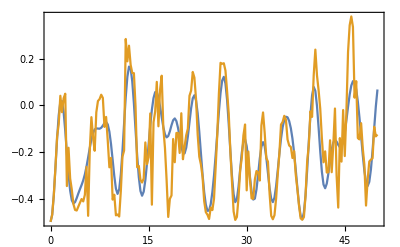

```mathematica
ListPlot[{Szt,varSzList},Frame->True,PlotRange->All,Joined->True]
```